## Configuration

```mathematica
Quiet[Needs["HypExp`"]];
Quiet[NotebookEvaluate["/Users/Matt/Documents/Research/MIW_mathematica/MIW_header_file.nb"]];

(* 

This notebook calculates the order(alpha_s tau) rate for each operator combination, in each region, and matches them onto the necessary soft operators
with the matching equation int_dPhi O^i(u1) M O^j(u2) = C^ij_k(mu/muJ) S_k(mu/muS;u1,u2)/(Sqrt[tau Q^2])^[k] , with no convolution in tau 

*)
```

*-*-*-*-*-* HPL 2.0 *-*-*-*-*-*

Author: Daniel Maitre, University of Zurich

Rules for minimal set loaded for weights: 2, 3, 4, 5, 6.

Rules for minimal set for + - weights loaded for weights: 2, 3, 4, 5, 6.

Table of MZVs loaded up to weight 6

Table of values at I loaded up to weight 6

$HPLFunctions gives a list of the functions of the package.
$HPLOptions gives a list of the options of the package.

More info in hep-ph/0507152, hep-ph/0703052 and at 
 http://krone.physik.unizh.ch/~maitreda/HPL/

***********************************
***********  HypExp 2.0  ************
***********************************
Authors:
 Tobias Huber:  RWTH Aachen,

Daniel Maitre: SLAC, University of Zurich.

HypExp loaded! It allows the expansion of hypergeometric functions around their parameters. 
 The new provided commands are:
 - HypExp
 - HypExpInt
 - HypExpU
 - HypExpAddToLib
 - HypExpIsKnownToOrder

More info in hep-ph/0507094 and at 
 http://krone.physik.unizh.ch/~maitreda/HypExp/

Loading FeynCalc from /Users/Matt/Library/Mathematica/Applications/HighEnergyPhysics

FeynCalc 8.2.0 For help, type ?FeynCalc, open FeynCalcRef8.nb or visit www.feyncalc.org

Loading FeynArts, see www.feynarts.de for documentation

FeynArts 3.7 patched for use with FeynCalc

Epsilon divergences for perp integrals with non-zero masses

div A0: 2/((D-4) π)

div A1: 0

div A00: m10/((D-4) π)

div A11: 0

div A001: 0

div A111: 0

div A0000: m10^2/(4 (D-4) π)

div A0011: 0

div A1111: 0

div A00001: 0

div A00111: 0

div A11111: 0

div B0: 0

div B1: 0

div B00: 1/((D-4) π)

div B11: 0

div B001: -1/(2 (D-4) π)

div B111: 0

div B0000: (3 (m10+m20)-p10)/(12 (D-4) π)

div B0011: 1/(3 (D-4) π)

div B1111: 0

div B00001: (-2 m10-4 m20+p10)/(24 (D-4) π)

div B00111: -1/(4 (D-4) π)

div B11111: 0

```mathematica
timeLimit=0.5;(* in minutes *)(* set this higher overnight *)
timeLimit=timeLimit*60;
$LimitTo4//myPrint
turnOffConditional[];
```

$LimitTo4=False

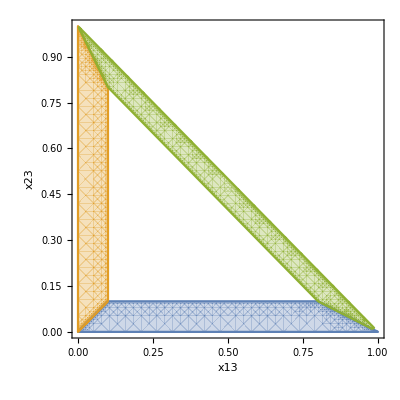

```mathematica
$Assumptions=0<eps<1/10 && 0<M<Q && 0<p1m<Q&&0<p1p<Q&&0<p2m<Q&&0<p2p<Q&&0<qm<Q&&0<qp<Q&&km∈Reals&&0≤ x≤ 1&&0≤ y≤ 1&&0≤ z≤ 1&&0≤ w≤ 1/3&&p3p∈Reals&&p3m∈Reals&&p4p∈Reals&&p4m∈Reals&&lambda∈Reals&&Q>0&&1/3>tau>0&&muMS>0&&1/3>tau>0&&0<qhatp<1&&0<qhatm<1;

replSingVarPlus[e_]:=e/.PlusDistribution[a_*HeavisideTheta[b_]]:>HeavisideTheta[b-beta]a+DiracDelta[b-beta]Integrate[a,{tau,1,tau}]/.PlusDistribution[a_]:>HeavisideTheta[tau-beta]a+DiracDelta[tau-beta]Integrate[a,{tau,1,tau}];

expLogs[e_]:=e//.Log[a_/b_]:>Log[a]-Log[b]//.Log[a_*b_]:>Log[a]+Log[b]/.Log[a_^n_]:>  n*Log[a];
dimensionalize[e_]:=e/.qhatm->qm/Q/.qhatp->qp/Q/.p1hatm->p1m/Q/.p1hatp->p1p/Q/.p2hatm->p2m/Q/.p2hatp->p2p/Q;


(* kinematics for p1m=0 *)
regBkinematics[e_]:=dimensionalize[e]/.Vperp[p2]->-Vperp[q]/.Vperp[p1]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-qhatm/.p2hatp->qhatp*qhatm/(1-qhatm)/.p1hatp->qhatm*(1-qhatp/(1-qhatm))/.p1hatm->0/.qhatp->x23*(1-qhatm)/.qhatm->x13/(1-x23);

(* kinematics for p2m=0 *)
regAkinematics[e_]:=dimensionalize[e]/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.qhatp->x13*(1-qhatm)/.qhatm->x23/(1-x13);
(* kinematics for p2m=0 *)
(*regAkinematics[e_]:=dimensionalize[e]/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p1hatm->1-qhatm/.p2hatp->(1-qhatp/(1-qhatm))/.p1hatp->qhatp*qhatm/(1-qhatm)/.p2hatm->0/.qhatp->x13*(1-qhatm)(*/.qhatm->x23/(1-x13)*);*)

(* kinematics for qm=0 *)
regCkinematics[e_]:=dimensionalize[e]/.Vperp[p2]->-Vperp[p1]/.Vperp[q]->0/.p1m->Q*p1hatm/.p2m->Q*p2hatm/.qm->Q*qhatm/.p1p->Q*p1hatp/.p2p->Q*p2hatp/.qp->Q*qhatp/.p2hatm->1-p1hatm/.p2hatp->p1hatp*p1hatm/(1-p1hatm)/.qhatp->qhatm*(1-p1hatp/(1-p1hatm))/.qhatm->0/.p1hatp->(1-p1hatm)(1-x13/p1hatm)/.p1hatm->x13/(x13+x23);

(* options *)
onlyLO=True;
onlyNLO=False;
doCheckLeftoverIntegrals=False;

prefac=g^2*Cf;

phasespaceA=0;
phasespaceB=0;
phasespaceC=0;

(* 
  angularity definitions in the three regions of Dalitz-space 
*)
fA[x13_,x23_,a_]:=(x13 (x13+x23-1) (-x23/(x13 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x13-1)
fB[x13_,x23_,a_]:=(x23 (x13+x23-1) (-x13/(x23 (x13+x23-1)))^(a/2)-x13 x23 (-(x13+x23-1)/(x13 x23))^(a/2))/(x23-1)
fC[x13_,x23_,a_]:=-((x13+x23-1) (x23 (-x13/(x23 (x13+x23-1)))^(a/2)+x13 (-x23/(x13 (x13+x23-1)))^(a/2)))/(x13+x23)
(* plot the thing *)
tautau=0.1;
aa=0;
RegionPlot[{2x13+x23<1&&x13+x23<1&&x23>x13&&0<fA[x13,x23,aa]<tautau,x13+2x23<1&&x13+x23<1&&x13>x23&&0<fB[x13,x23,aa]<tautau,2x13+x23>1&&x13+2x23>1&&x13+x23<1&&0<fC[x13,x23,aa]<tautau},{x23,0,1},{x13,0,1},AxesLabel-> {x13,x23},MaxRecursion->5]

Unprotect[Tr];
Tr/:Tr[0]:=0;
Protect[Tr];

spinSumHornig=MTD[alpha,beta](MTD[mu,nu]-FVD[n+nb,mu]FVD[n+nb,nu]/4);
spinSumTranseverse=MTD[alpha,beta](MTD[mu,nu]-FVD[nb,mu]FVD[n,nu]/2-FVD[n,mu]FVD[nb,nu]/2);
spinSumSimple=MTD[alpha,beta](MTD[mu,nu]);

spinSum=spinSumHornig;

phaseSpacePrefac=1/(64*Pi^2)*(4*Pi/(Q^2))^(+eps)/(Gamma[2-eps]);
c2=1+alphaMS*Cf*(-Log[(-Q^2+I*delta)/muMS^2]^2+3*Log[(-Q^2+I*delta)/muMS^2]+Pi^2/6-8)/(4*Pi);
Z2=1+Cf*alphaMS(2/eps^2+(-2*Log[(-Q^2+I*delta)/muMS^2]+3)/eps)/(4*Pi);
```

## Expressions for Integration Regions

### Phase Space Integrals

#### A -- Sideways Integration (x-first)

```mathematica
(* try integrating x first, then y *)

(*
regAs1=Integrate[x^(n-1+eps)(1-x-y)^(eps),{x,y,1-2*y}];
regAs2=Integrate[%*y^(m-1+eps),{y,0,tau}];
regAs3=Series[%,{tau,0,2}]//Normal;
*)

(* it worked but the output is HUGE! Almost 57000 terms long *)

(* instead of keeping the huge result, we'll store the 4x4 {n,m} elements that are necessary for usual calculations *)
(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regA00=-Pi^2/6+1/(2*ϵ^2)-2*τ-Log[τ]^2/2; 
regA01=τ*(1-Log[τ]);
regA02=0;
regA03=0;

regA10=-2+ϵ^(-1)-3*τ+Log[τ];
regA11=τ;
regA12=0;
regA13=0;

regA20=-1+1/(2*ϵ)-2*τ+Log[τ]/2;
regA21=τ/2;
regA22=0;
regA23=0;

regA30=-13/18+1/(3*ϵ)-2*τ+Log[τ]/3;
regA31=τ/3;
regA32=0;
regA33=0;
```

```mathematica
(*
Integrate[x^(0-1+eps)(1-x-y)^(eps),{x,y,1-2*y}]
Integrate[%*y^(0-1+eps),{y,0,tau}]
Series[%,{tau,0,4}]//Normal

Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
*)
```

#### B -- Vertical Integration (y-first)

```mathematica
(* summary *)

regB00=regA00;
regB01=regA10;
regB02=regA20;
regB03=regA30;

regB10=regA01;
regB11=regA11;
regB12=regA21;
regB13=regA31;

regB20=regA02;
regB21=regA12;
regB22=regA22;
regB23=regA32;

regB30=regA03;
regB31=regA13;
regB32=regA23;
regB33=regA33;
```

```mathematica
(*
Integrate[y^(m-1+eps)(1-x-y)^(eps),{y,x,1-2*x}]
Integrate[%*x^(n-1+eps),{x,0,tau}]
regBlong=Series[%,{tau,0,2}]//Normal
*)

(* this is equivalent to the region A integration, but with n interchanged with m *)
```

#### C -- Sideways Integration (x-first)

```mathematica
(* summary *)

(* it looks like I only need to know the result for c02, c11, and c20, so let's just do those *)

(* remember, the epsilons here are IR regulators, so negative. Later, use /.eps->negeps/.negeps->-eps to revert back to regular epsilons *)

regC00=τ*(2-2*Log[τ]);
regC01=τ-τ*Log[τ];
regC02=-(τ*Log[τ]);
regC03=τ*(-1/2-Log[τ]);

regC10=τ*(1-Log[τ]);
regC11=τ;
regC12=τ/2;
regC13=τ/3;

regC20=-(τ*Log[τ]);
regC21=τ/2;
regC22=τ/6;
regC23=τ/12;

regC30=-(τ*(1+2*Log[τ]))/2;
regC31=τ/3;
regC32=τ/12;
regC33=τ/30;
```

```mathematica
(* convert integrals from y to u=1-x-y *)
(* then the integration region has the same form as region A so we can try the sideways integration again *)

(*nn=1;
mm=1;

regCs02i=Integrate[x^(nn-1+eps)(1-x-u)^(mm-1+eps),{x,u,1-2*u}]

%/.Hypergeometric2F1Regularized[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1Regularized[a,b,c,d],eps,2]/.Hypergeometric2F1[a_,b_,c_,d_]:>HypExp[Hypergeometric2F1[a,b,c,d],eps,2]/.Beta[z_,a_,b_]:>(z^a/a)*HypExp[Hypergeometric2F1[a,1-b,1+a,z],eps,2]

regCs02ii=Integrate[%*u^eps,{u,0,tau}]
regCs02=Series[%,{tau,0,2}];
regCs02=Series[%,{tau,0,1}]//Normal;
regCs02=Series[%,{eps,0,0}]//Normal
regCsnnmm=Series[%,{tau,0,1}]//Normal
regCsnnmm//InputForm*)
```

#### Overall

```mathematica
int00=regA00+regB00+regC00;
int01=regA01+regB01+regC01;
int02=regA02+regB02+regC02;
int03=regA03+regB03+regC03;

int10=regA10+regB10+regC10;
int11=regA11+regB11+regC11;
int12=regA12+regB12+regC12;
int13=regA13+regB13+regC13;

int20=regA20+regB20+regC20;
int21=regA21+regB21+regC21;
int22=regA22+regB22+regC22;
int23=regA23+regB23+regC23;

int30=regA30+regB30+regC30;
int31=regA31+regB31+regC31;
int32=regA32+regB32+regC32;
int33=regA33+regB33+regC33;
```

```mathematica
gamma=u*(1-u)*DiracDelta[u-w]+u*w^2*(1-w)-3*u^2*(1-u)*w/4 - 3*u*w/80
c=DiracDelta[a-w]+b*w

c*gamma//Expand
%/.DiracDelta[a_]*DiracDelta[b_]:>Inactive[DiracDelta][a]*DiracDelta[b]
Integrate[%,{w,0,1},Assumptions->0<a<1&&0<u<1&&0<b<1]
%/.b->a//Activate
Collect2[%,DiracDelta[_]]
%//Expand
%/.DiracDelta[_]->0
%/(a*u)//Expand
```

(1-u) u u-w-3/4 (1-u) u^2 w+u (1-w) w^2-(3 u w)/80

a-w+b w

3/4 u^3 w a-w-3/4 u^2 w a-w-u^2 a-w u-w-u w^3 a-w+u w^2 a-w-3/80 u w a-w+u a-w u-w-b u^2 w u-w+b u w u-w+3/4 b u^3 w^2-3/4 b u^2 w^2-b u w^4+b u w^3-3/80 b u w^2

-u^2 u-w δ[a-w]+u u-w δ[a-w]+3/4 u^3 w a-w-3/4 u^2 w a-w-u w^3 a-w+u w^2 a-w-3/80 u w a-w-b u^2 w u-w+b u w u-w+3/4 b u^3 w^2-3/4 b u^2 w^2-b u w^4+b u w^3-3/80 b u w^2

u^2 (-δ[a-u])+u δ[a-u]+1/80 u (-80 a^3+80 a^2+a (60 u^2-60 u-3)+3 b (-20 u^2+20 u+1))

1/80 u (-80 a^3+80 a^2+3 a (-20 u^2+20 u+1)+a (60 u^2-60 u-3))+u^2 (-a-u)+u a-u

-(a-1) a^2 u-(u-1) u a-u

a^3 (-u)+a^2 u-u^2 a-u+u a-u

a^2 u-a^3 u

a-a^2

## Subsubleading Order

```mathematica
(* Recall the factorization formula : *)

(* int d_phi O_2^i Mhat O_2^j = int_0^tau C_s^ijk S^k + tau*int_0^tau C_Stau^ij S^0 *)
```

### Contributions from A-type operators

```mathematica
(* operator vevs *)
```

```mathematica
ampO20a=-I*g*Ta*SpinorUBar[p1].(  (2*FVD[p1,alpha]+GAD[alpha].GSD[q])/(2*SPD[p1,q])-FVD[nb,alpha]/SPD[nb,q]).Phatnb.GAD[mu].Phatnb.SpinorV[p2]
ampO21a=I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].(GSD[n]/2).Vperp[GAD[rho]]-Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].Phatnb).SpinorV[p2]*Deltabarq[alpha,rho]*DiracDelta[u1-qhatm]//DeltaDef
ampO22a1=-I*g*Ta*SpinorUBar[p1].(Phatnb.GAD[mu].Phatnb.Vperp[GAD[rho]].Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]*DiracDelta[u1-qhatm]//DeltaDef
ampO22a2=-I*g*Ta*SpinorUBar[p1].(Vperp[GAD[rho]].(GSD[nb]/2).GAD[mu].(GSD[n]/2).Vperp[GAD[sigma]]).SpinorV[p2]*FVD[q,rho]*Deltabarq[alpha,sigma]*DiracDelta[u1-p1hatm]//DeltaDef

ampDagO20a=I*g*Tb*SpinorVBar[p2].Phatn.GAD[nu].Phatn.(  (2*FVD[p1,beta]+GSD[q].GAD[beta])/(2*SPD[p1,q])-FVD[nb,beta]/SPD[nb,q]).SpinorU[p1]//DeltaDef;
ampDagO21a=-I*g*Tb*SpinorVBar[p2].(Phatn.GAD[nu].(GSD[nb]/2).Vperp[GAD[phi]]-Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].Phatn).SpinorU[p1]*Deltabarq[beta,phi]*DiracDelta[u2-qhatm]//DeltaDef;
ampDagO22a1=I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].Vperp[GAD[psi]].Phatn.GAD[nu].Phatn).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]*DiracDelta[u2-qhatm]//DeltaDef;
ampDagO22a2=I*g*Tb*SpinorVBar[p2].(Vperp[GAD[phi]].(GSD[n]/2).GAD[nu].(GSD[nb]/2).Vperp[GAD[psi]]).SpinorU[p1]*FVD[q,psi]*Deltabarq[beta,phi]*DiracDelta[u2-p1hatm]//DeltaDef;
```

-ⅈ g Ta SpinorUBar(p1).((2 FVD(p1,alpha)+GAD(alpha).GSD(q))/(2 SPD(p1,q))-(FVD(nb,alpha))/(SPD(nb,q))).Phatnb.GAD(mu).Phatnb.SpinorV(p2)

ⅈ g Ta u1-qhatm Deltabarq(alpha,rho) SpinorUBar(p1).(Phatnb.GAD(mu).(GSD(n))/2.Vperp(GAD(rho))-Vperp(GAD(rho)).(GSD(nb))/2.GAD(mu).Phatnb).SpinorV(p2)

-ⅈ g Ta u1-qhatm Deltabarq(alpha,sigma) FVD(q,rho) SpinorUBar(p1).Phatnb.GAD(mu).Phatnb.Vperp(GAD(rho)).Vperp(GAD(sigma)).SpinorV(p2)

-ⅈ g Ta u1-p1hatm Deltabarq(alpha,sigma) FVD(q,rho) SpinorUBar(p1).Vperp(GAD(rho)).(GSD(nb))/2.GAD(mu).(GSD(n))/2.Vperp(GAD(sigma)).SpinorV(p2)

ⅈ g Ta u1-p1hatm (MTD(alpha,rho)-(FVD(n,alpha) FVD(q,rho))/(SPD(n,q))) SpinorUBar(p1).Phatnb.GAD(mu).(GSD(nb))/2.Vperp(GAD(rho)).SpinorV(p2)

#### < O20a | O20a >

```mathematica
ampO20aO20a=GSD[p2].ampDagO20a.GSD[p1].ampO20a*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;
(*ampO20aO20a=GSD[p2].ampDagO20a.GSD[p1].ampO20a*MTD[alpha,beta]/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;*)

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO20a=(Tr[%]//FCE//DiracSimplify//FCE); 

dTraceO20aO20a//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO20afinite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO20a=O20aO20afinite/.eps->negeps/.negeps->-eps  /. MTD[a_,b_]:>Vperp[MTD[a,b]]+FVD[n,a]FVD[nb,b]/2+FVD[n,b]FVD[nb,a]/2//Simplify(* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO20a00=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,0}];
O20aO20a10=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,0}];
O20aO20a20=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,0}];
O20aO20a30=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,0}];

O20aO20a01=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,1}];
O20aO20a11=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,1}];
O20aO20a21=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,1}];
O20aO20a31=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,1}];

O20aO20a02=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,2}];
O20aO20a12=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,2}];
O20aO20a22=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,2}];
O20aO20a32=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,2}];

O20aO20a03=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,0},{x13,0,3}];
O20aO20a13=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,1},{x13,0,3}];
O20aO20a23=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,2},{x13,0,3}];
O20aO20a33=SeriesCoefficient[krabbyO20aO20a*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO20a={{O20aO20a00,O20aO20a01,O20aO20a02,O20aO20a03},{O20aO20a10,O20aO20a11,O20aO20a12,O20aO20a13},{O20aO20a20,O20aO20a21,O20aO20a22,O20aO20a23},{O20aO20a30,O20aO20a31,O20aO20a32,O20aO20a33}}
checksumO20aO20a=krabbyO20aO20a*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO20a.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO20a=0;
totalO20aO20a+=O20aO20a00*regA00+O20aO20a01*regA01+O20aO20a02*regA02+O20aO20a03*regA03;
totalO20aO20a+=O20aO20a10*regA10+O20aO20a11*regA11+O20aO20a12*regA12+O20aO20a13*regA13;
totalO20aO20a+=O20aO20a20*regA20+O20aO20a21*regA21+O20aO20a22*regA22+O20aO20a23*regA23;
totalO20aO20a+=O20aO20a30*regA30+O20aO20a31*regA31+O20aO20a32*regA32+O20aO20a33*regA33;
totalO20aO20a=totalO20aO20a/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)

(* the factor of two comes from the equal contribution in the B sector that must be included since O20 doesnt set the gluon quantum number *)
contributionO20aO20a=1*(1/Z2)*ComplexConjugate[1/Z2]+2*phaseSpacePrefac*totalO20aO20a; 

%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO20a=%//Expand
```

(8 g^2 C_F (2 x13^2 (ϵ+1)+2 x13 (x23-2) (ϵ+1)+x23^2 (2 ϵ+1)-2 x23 (ϵ+1)+2 (ϵ+1)))/(x13 x23)

(16 C_F g^2+16 C_F ϵ g^2 | -32 C_F g^2 (ϵ+1) | 16 C_F g^2 (ϵ+1) | 0
-16 C_F g^2-16 C_F ϵ g^2 | 16 C_F g^2+16 C_F ϵ g^2 | 0 | 0
8 C_F g^2 (2 ϵ+1) | 0 | 0 | 0
0 | 0 | 0 | 0)

0

(4 g^2 C_F (3 ϵ^2 log(τ) (8 τ+(2-8 τ) ϵ+2 (ϵ-1) log(τ)-3)+ϵ (2 ϵ (6 τ (2 ϵ-1)+(π^2-6) (ϵ-1))+3)+6))/(3 ϵ^2)

-(2 τ C_F α_OverBar[MS])/π-(C_F α_OverBar[MS] log^2(τ))/π+(4 τ C_F α_OverBar[MS] log(τ))/π-(3 C_F α_OverBar[MS] log(τ))/(2 π)-5/12 π C_F α_OverBar[MS]+(7 C_F α_OverBar[MS])/(2 π)+(C_F α_OverBar[MS] log(1/Q^2))/(π ϵ)+(C_F α_OverBar[MS] log^2(1/Q^2))/(2 π)+(3 C_F α_OverBar[MS] log(1/Q^2))/(2 π)+(C_F α_OverBar[MS] log((-Q^2-ⅈ δ)/μ_OverBar[MS]^2))/(2 π ϵ)+(C_F α_OverBar[MS] log((-Q^2+ⅈ δ)/μ_OverBar[MS]^2))/(2 π ϵ)+(C_F α_OverBar[MS] log(1/Q^2) log(μ_OverBar[MS]^2))/π+(C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(π ϵ)+(C_F α_OverBar[MS] log^2(μ_OverBar[MS]^2))/(2 π)+(3 C_F α_OverBar[MS] log(μ_OverBar[MS]^2))/(2 π)+1

```mathematica
contributionO20aO20a//expLogs//Expand
%//InputForm
```

-(τ C_F α_OverBar[MS])/π-(C_F α_OverBar[MS] log^2(τ))/(2 π)+(2 τ C_F α_OverBar[MS] log(τ))/π-(3 C_F α_OverBar[MS] log(τ))/(4 π)+(C_F α_OverBar[MS])/(2 π ϵ^2)+(3 C_F α_OverBar[MS])/(4 π ϵ)-5/24 π C_F α_OverBar[MS]+(7 C_F α_OverBar[MS])/(4 π)-(C_F α_OverBar[MS] log(Q))/(π ϵ)+(C_F α_OverBar[MS] log^2(Q))/π-(3 C_F α_OverBar[MS] log(Q))/(2 π)-(2 C_F α_OverBar[MS] log(Q) log(μ_OverBar[MS]))/π+(C_F α_OverBar[MS] log(μ_OverBar[MS]))/(π ϵ)+(C_F α_OverBar[MS] log^2(μ_OverBar[MS]))/π+(3 C_F α_OverBar[MS] log(μ_OverBar[MS]))/(2 π)

(7*alphaMS*Cf)/(4*Pi) - (5*alphaMS*Cf*Pi)/24 + (alphaMS*Cf)/(2*Pi*ϵ^2) + (3*alphaMS*Cf)/(4*Pi*ϵ) - (alphaMS*Cf*τ)/Pi + (3*alphaMS*Cf*Log[muMS])/(2*Pi) + (alphaMS*Cf*Log[muMS])/(Pi*ϵ) + (alphaMS*Cf*Log[muMS]^2)/Pi - 
 (3*alphaMS*Cf*Log[Q])/(2*Pi) - (alphaMS*Cf*Log[Q])/(Pi*ϵ) - (2*alphaMS*Cf*Log[muMS]*Log[Q])/Pi + (alphaMS*Cf*Log[Q]^2)/Pi - (3*alphaMS*Cf*Log[τ])/(4*Pi) + (2*alphaMS*Cf*τ*Log[τ])/Pi - (alphaMS*Cf*Log[τ]^2)/(2*Pi)

```mathematica
contributionO20aO20a/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO20a=(Series[%,{tau,0,1}]//Normal//Expand)/.Log[Q]->LQ/2+Log[muMS](*/.Log[tau]^2->( ( LS-LQ)/2  )( LJ-LQ)*) //Simplify
```

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ log((-Q^2-ⅈ δ)/μ_OverBar[MS]^2))/ϵ+(ᾱ log((-Q^2+ⅈ δ)/μ_OverBar[MS]^2))/ϵ+2 ᾱ log(1/Q^2) log(μ_OverBar[MS]^2)+(2 ᾱ log(μ_OverBar[MS]^2))/ϵ+ᾱ log^2(μ_OverBar[MS]^2)+3 ᾱ log(μ_OverBar[MS]^2)+(2 ᾱ log(1/Q^2))/ϵ+ᾱ log^2(1/Q^2)+3 ᾱ log(1/Q^2)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ (-2 log(μ_OverBar[MS])+log(-Q^2-ⅈ δ)))/ϵ+(ᾱ (-2 log(μ_OverBar[MS])+log(-Q^2+ⅈ δ)))/ϵ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+(ᾱ (-2 log(μ_OverBar[MS])+2 log(Q)-ⅈ π))/ϵ+(ᾱ (-2 log(μ_OverBar[MS])+2 log(Q)+ⅈ π))/ϵ-8 ᾱ log(Q) log(μ_OverBar[MS])+(4 ᾱ log(μ_OverBar[MS]))/ϵ+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])-(4 ᾱ log(Q))/ϵ+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

ᾱ (LQ^2-3 LQ-4 τ-2 log^2(τ)+(8 τ-3) log(τ)-(5 π^2)/6+7)+1

```mathematica
finalO20aO20a//Expand
```

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+LQ^2 ᾱ-3 LQ ᾱ+1

```mathematica
softVev0=1+alphabar*(Pi^2/6-Log[tau^2*Q^2/muMS^2]^2)
softC00to0=1+alphabar*(2Log[tau*Q^2/muMS^2]^2-3Log[tau*Q^2/muMS^2]-Pi^2+7)(*+alphabar*tau*(Aa+Bb*Log[tau*Q^2/muMS^2]+Cc*Log[tau*Q^2/muMS^2]^2)*)
softVev0*softC00to0
Series[%,{alphabar,0,1}]//Normal
softTimesCoeff=%/.Log[Q]->LQ/2+Log[muMS]//expLogs//Expand
```

ᾱ (π^2/6-log^2((Q^2 τ^2)/μ_OverBar[MS]^2))+1

ᾱ (2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-π^2+7)+1

(ᾱ (2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-π^2+7)+1) (ᾱ (π^2/6-log^2((Q^2 τ^2)/μ_OverBar[MS]^2))+1)

ᾱ (-log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-(5 π^2)/6+7)+1

-2 ᾱ log^2(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ-8 ᾱ log(Q) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

```mathematica
%/.Log[Q]->LQ/2+Log[muMS]//Expand
%-finalO20aO20a//Expand
```

-2 ᾱ log^2(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+LQ^2 ᾱ-3 LQ ᾱ+1

4 τ ᾱ-8 τ ᾱ log(τ)

```mathematica
softTimesCoeff-finalO20aO20a/.LQ->Log[Q^2/muMS^2]//expLogs//Expand
```

4 τ ᾱ-8 τ ᾱ log(τ)

```mathematica
(* the soft functions must match onto the above result:

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)+(π^2 ᾱ)/3-ᾱ+1
which is what we get from |C_2|^2 <O_2^0|O_2^0> 
*)

softVev0=1+alphabar*(Pi^2/6-Log[tau^2*Q^2/muMS^2]^2)
softCoeff0 = 1+alphabar*(2Log[tau*Q^2/muMS^2]^2-3Log[tau*Q^2/muMS^2]-Pi^2+7)-8*alphabar*tau*Log[tau*Q^2/muMS^2]
(*softCTerm0=DiracDelta[tau-delta](1-2alphabar(1/eps^2-LQ/eps))+4*alphabar*PlusDistribution[HeavisideTheta[tau]/tau]/eps;
softFinite0=DiracDelta[-δ+τ]-LQ^2*DiracDelta[-δ+τ]*alphabar+(Pi^2*DiracDelta[-δ+τ]*OverBar[α])/6-4*alphabar*(LQ*PlusDistribution[τ^(-1)]+2*PlusDistribution[Log[τ]/τ])
softVev0=softCTerm0+softFinite0-DiracDelta[tau-delta];

Series[softCoeff0*softFinite0//Expand,{alphabar,0,1}]//Normal;
contributionIgrand=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,1}]+Integrate[SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,0}],{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%(**c2*ComplexConjugate[c2]*)/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont0=Limit[%,delta->0]//expLogs//Expand*)
cont0=Series[softVev0*softCoeff0,{alphabar,0,1}]//Normal

checkLO=finalO20aO20a-cont0
(* still missing terms proportional to tau: need subleading soft operators *)





(* soft operator 2M is the same field content with measurement operator Mhat=-kp*km*(D@DiracDelta[tau-kp]Theta[km-kp]+D@DiracDelta[tau-km]Theta[kp-km]) *)
softCoeff2M=5
softCTerm2M=0;
softFinite2M=4*alphabar*tau
softVev2M=4*alphabar*tau;

(*Series[softCoeff2M*softFinite2M//Expand,{alphabar,0,1}]//Normal;
contributionIgrand2M=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution2M=Integrate[contributionIgrand2M,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2M=Limit[%,delta->0]//expLogs//Expand*)
cont2M=softCoeff2M*softVev2M

(* soft operator 2A1 is W_nb^dag (iD)^2(x+nb*t) W_n^dag W_nb *)
softCoeff2A1=4
softCTerm2A1=0;(* needs anomalous dimension matrix *)
softFinite2A1=2alphabar(LS-1)
softVev2A1=2alphabar(LS)*tau;
(*
Series[softCoeff2A1*softFinite2A1//Expand,{alphabar,0,1}]//Normal
contributionIgrand2A1=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=Integrate[contributionIgrand2A1,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2A1=Limit[%,delta->0]//expLogs//Expand*)

checkNLO=finalO20aO20a-cont0-cont2A1-cont2M
```

ᾱ (π^2/6-log^2((Q^2 τ^2)/μ_OverBar[MS]^2))+1

ᾱ (2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-π^2+7)-8 τ ᾱ log((Q^2 τ)/μ_OverBar[MS]^2)+1

ᾱ (-log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-8 τ log((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-(5 π^2)/6+7)+1

ᾱ (LQ^2-3 LQ-4 τ-2 log^2(τ)+(8 τ-3) log(τ)-(5 π^2)/6+7)-ᾱ (-log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-8 τ log((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-(5 π^2)/6+7)

5

4 τ ᾱ

20 τ ᾱ

4

2 (LS-1) ᾱ

-20 τ ᾱ+ᾱ (LQ^2-3 LQ-4 τ-2 log^2(τ)+(8 τ-3) log(τ)-(5 π^2)/6+7)-ᾱ (-log^2((Q^2 τ^2)/μ_OverBar[MS]^2)+2 log^2((Q^2 τ)/μ_OverBar[MS]^2)-8 τ log((Q^2 τ)/μ_OverBar[MS]^2)-3 log((Q^2 τ)/μ_OverBar[MS]^2)-(5 π^2)/6+7)-cont2A1

```mathematica
checkLO//expLogs//Expand
%/.LQ->2Log[Q]-2Log[muMS]//Expand
```

-4 τ ᾱ+16 τ ᾱ log(τ)+LQ^2 ᾱ-3 LQ ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-16 τ ᾱ log(μ_OverBar[MS])-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+16 τ ᾱ log(Q)-4 ᾱ log^2(Q)+6 ᾱ log(Q)

-4 τ ᾱ+16 τ ᾱ log(τ)-16 τ ᾱ log(μ_OverBar[MS])+16 τ ᾱ log(Q)

```mathematica
checkNLO//expLogs//Expand
%/.LQ->2Log[Q]-2Log[muMS]//Expand
```

-24 τ ᾱ+16 τ ᾱ log(τ)+LQ^2 ᾱ-3 LQ ᾱ+8 ᾱ log(Q) log(μ_OverBar[MS])-16 τ ᾱ log(μ_OverBar[MS])-4 ᾱ log^2(μ_OverBar[MS])-6 ᾱ log(μ_OverBar[MS])+16 τ ᾱ log(Q)-4 ᾱ log^2(Q)+6 ᾱ log(Q)-cont2A1

-24 τ ᾱ+16 τ ᾱ log(τ)-16 τ ᾱ log(μ_OverBar[MS])+16 τ ᾱ log(Q)-cont2A1

```mathematica
(* for figuring out matching coefficients *)
eq1=SeriesCoefficient[checkNLO,{Log[muMS],0,1}]
eq2=SeriesCoefficient[checkNLO,{Log[tau],0,1}]
eq3=SeriesCoefficient[checkNLO,{Log[_],0,0}]

Solve[{eq1,eq2,eq3}=={0,0,0},{A,B,R}]
```

0

8 τ ᾱ-3 ᾱ

ᾱ (LQ^2-3 LQ-24 τ)-cont2A1

{}

#### < O20a | O21a > + < O21a | O20a >

```mathematica
ampO20aO21a=(GSD[p2].ampDagO20a.GSD[p1].ampO21a+GSD[p2].ampDagO21a.GSD[p1].ampO20a)*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a

%//DiracSimplify//FCE
%/.Ta*Tb->Cf//PhatDef//lcCompAll
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE
%//gPerpDef
dTraceO20aO21a=Tr[%]//FCE//DiracSimplify//FCE  

dTraceO20aO21a//regAkinematics
%//Simplify
%/.D->4-2*eps//Simplify
O20aO21afinite=Series[%,{eps,0,1}]//Normal

krabbyO20aO21a=O20aO21afinite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO21a00=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,0}];
O20aO21a10=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,0}];
O20aO21a20=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,0}];
O20aO21a30=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,0}];

O20aO21a01=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,1}];
O20aO21a11=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,1}];
O20aO21a21=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,1}];
O20aO21a31=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,1}];

O20aO21a02=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,2}];
O20aO21a12=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,2}];
O20aO21a22=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,2}];
O20aO21a32=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,2}];

O20aO21a03=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,0},{x13,0,3}];
O20aO21a13=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,1},{x13,0,3}];
O20aO21a23=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,2},{x13,0,3}];
O20aO21a33=SeriesCoefficient[krabbyO20aO21a*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO21a={{O20aO21a00,O20aO21a01,O20aO21a02,O20aO21a03},{O20aO21a10,O20aO21a11,O20aO21a12,O20aO21a13},{O20aO21a20,O20aO21a21,O20aO21a22,O20aO21a23},{O20aO21a30,O20aO21a31,O20aO21a32,O20aO21a33}}
checksumO20aO21a=krabbyO20aO21a*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO21a.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO21a=0;
totalO20aO21a+=O20aO21a00*regA00+O20aO21a01*regA01+O20aO21a02*regA02+O20aO21a03*regA03;
totalO20aO21a+=O20aO21a10*regA10+O20aO21a11*regA11+O20aO21a12*regA12+O20aO21a13*regA13;
totalO20aO21a+=O20aO21a20*regA20+O20aO21a21*regA21+O20aO21a22*regA22+O20aO21a23*regA23;
totalO20aO21a+=O20aO21a30*regA30+O20aO21a31*regA31+O20aO21a32*regA32+O20aO21a33*regA33;
totalO20aO21a=totalO20aO21a/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO20aO21a=phaseSpacePrefac*totalO20aO21a;
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO21a=%//Expand
```

g^αβ (g^μν-1/4 (n^μ+(n̄)^μ) (n^ν+(n̄)^ν)) ((γ·p_2).(ⅈ g T^b (P̂)_n.γ^ν.(P̂)_n.((2 p_1^β+(γ·q).γ^β)/(2 p_1·q)-(n̄)^β/q^-)).(γ·p_1).(ⅈ g T^a u1-OverHat[TraditionalForm`TraditionalForm`q]^- (g^αρ-((n̄)^α q^ρ)/q^-) ((P̂)_(n̄).γ^μ.(γ·n)/2.(γ^ρ)_⊥-(γ^ρ)_⊥.(γ·n̄)/2.γ^μ.(P̂)_(n̄)))+(γ·p_2).(-ⅈ g T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (g^βϕ-((n̄)^β q^ϕ)/q^-) ((P̂)_n.γ^ν.(γ·n̄)/2.(γ^ϕ)_⊥-(γ^ϕ)_⊥.(γ·n)/2.γ^ν.(P̂)_n)).(γ·p_1).(-ⅈ g T^a ((2 p_1^α+γ^α.(γ·q))/(2 p_1·q)-(n̄)^α/q^-).(P̂)_(n̄).γ^μ.(P̂)_(n̄)))

-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ν.(γ·n).(γ·p_1_⊥) g^2)/(2 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).γ^ν.(P̂)_(n̄) g^2)/(2 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).γ^ν.(P̂)_(n̄) g^2)/(2 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·p_1_⊥) g^2)/(8 p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) g^2)/(8 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).(γ·n).(P̂)_(n̄) g^2)/(8 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ·p_1_⊥).(γ·p_1).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) g^2)/(8 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·p_1_⊥) g^2)/(8 p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·p_1).(γ·p_1_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) g^2)/(8 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·p_1_⊥).(γ·n).γ^ν.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ν.(P̂)_(n̄) g^2)/(2 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·p_1_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n).(P̂)_(n̄) g^2)/(8 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·p_1_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) g^2)/(8 p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(P̂)_(n̄).γ^ν.(γ·n).(γ^ρ)_⊥ g^2)/(4 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).γ^ν.(P̂)_(n̄) g^2)/(4 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(γ·n̄).(γ^ϕ)_⊥.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).γ^ν.(P̂)_(n̄) g^2)/(4 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ^ρ)_⊥ g^2)/(16 p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).(γ·n).(P̂)_(n̄) g^2)/(16 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ^ϕ)_⊥.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).(γ·n).(P̂)_(n̄) g^2)/(16 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ^ϕ)_⊥.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) g^2)/(16 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ^ρ)_⊥ g^2)/(16 p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·q).γ^ρ.(γ·p_1).(γ^ρ)_⊥.(γ·n̄).(γ·n).(P̂)_(n̄) g^2)/(16 p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ^ϕ)_⊥.(γ·n).γ^ν.(P̂)_n.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).γ^ν.(P̂)_(n̄) g^2)/(4 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ^ϕ)_⊥.(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).(γ·n).(P̂)_(n̄) g^2)/(16 p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ^ϕ)_⊥.(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).γ^ϕ.(γ·q).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) g^2)/(16 p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).γ^ν.(γ·n).(γ·q_⊥) g^2)/(4 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·q_⊥) g^2)/(16 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·q).(γ·n̄).(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·q_⊥) g^2)/(16 q^- p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).γ^ν.(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).γ^ν.(P̂)_(n̄) g^2)/(4 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·n).(P̂)_(n̄) g^2)/(16 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) g^2)/(16 q^- p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ν.(γ·n).(γ·q_⊥) p_1^- g^2)/(2 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).γ^ν.(P̂)_(n̄) p_1^- g^2)/(2 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).γ^ν.(P̂)_(n̄) p_1^- g^2)/(2 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).γ^ν.(P̂)_(n̄) p_1^- g^2)/(2 q^- p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.γ^ν.(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).γ^ν.(P̂)_(n̄) p_1^- g^2)/(2 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·q_⊥) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n).(γ·q_⊥).(γ·n̄).(γ·q).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)-(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(γ·n).(γ·q_⊥) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·p_1).(γ·q_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(P̂)_n.(γ·n̄).(P̂)_n.(γ·q).(γ·q_⊥).(γ·n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)-(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).γ^ν.(P̂)_n.(γ·p_1).(P̂)_(n̄).γ^ν.(P̂)_(n̄) p_1^- g^2)/(2 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)+(T^a T^b u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2).(γ·q_⊥).(γ·n).(γ·n̄).(P̂)_n.(γ·p_1).(P̂)_(n̄).(γ·n̄).(P̂)_(n̄) p_1^- g^2)/(8 q^- p_1·q)

(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·p_1_⊥) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·p_1_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ·p_1_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ·p_1_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·p_1_⊥) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·p_1_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n).(γ·p_1_⊥) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·p_1_⊥).(γ·n̄).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n̄).(γ·p_1_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) g^2)/(8 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·p_1_⊥).(γ·n).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(2 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ^ρ)_⊥ g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ^ρ)_⊥.(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ^ϕ)_⊥.(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ^ϕ)_⊥.(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ^ρ)_⊥ g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ^ρ)_⊥.(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n).(γ^ρ)_⊥ g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(1/2 (n̄)^ρ γ·n+1/2 n^ρ γ·n̄+(γ^ρ)_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ^ρ)_⊥.(γ·n̄).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n̄).(γ^ϕ)_⊥.(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ^ϕ)_⊥.(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ^ϕ)_⊥.(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ^ϕ)_⊥.(γ·n).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(1/2 (n̄)^ϕ γ·n+1/2 n^ϕ γ·n̄+(γ^ϕ)_⊥).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·n̄).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·q_⊥) g^2)/(16 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·n̄).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·q_⊥) g^2)/(16 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·n̄).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n).(γ·q_⊥) g^2)/(4 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) g^2)/(16 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) g^2)/(16 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) g^2)/(4 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·q_⊥) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·q_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·q_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·n̄).(γ·q_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n).(γ·q_⊥).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·n).(γ·q_⊥) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·q_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·q_⊥).(γ·n̄).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n).(γ·q_⊥) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·q_⊥).(γ·n̄).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·q_⊥).(γ·n̄).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n̄).(γ·q_⊥).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·n/2).(γ·(n̄)/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·q_⊥).(γ·n̄).(γ·q_⊥+γ·(n̄)/2 q^++γ·n/2 q^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(γ·n̄).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(γ·n̄).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·p_2_⊥+γ·(n̄)/2 p_2^++γ·n/2 p_2^-).(γ·q_⊥).(γ·n).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·n/2).(γ·(n̄)/2).(γ·p_1_⊥+γ·(n̄)/2 p_1^++γ·n/2 p_1^-).(γ·(n̄)/2).(γ·n/2).(1/2 (n̄)^ν γ·n+1/2 n^ν γ·n̄+(γ^ν)_⊥).(γ·(n̄)/2).(γ·n/2) p_1^- g^2)/(2 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+p_1_⊥·q_⊥))

(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥ p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·q_⊥).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ g^2)/(512 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·q_⊥) p_2^+ p_1^- g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ·q_⊥).(γ·n).(γ^ν)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥ p_2^+ p_1^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^- g^2)/(512 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥ p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥.(γ·q_⊥).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·q_⊥).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥ p_2^+ p_1^- q^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n).(γ^ρ)_⊥.(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^- q^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ^ϕ)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_1^- p_2^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ^ν)_⊥.(γ·n).(γ·q_⊥) p_2^+ (p_1^-)^2 g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ·q_⊥).(γ·n).(γ^ν)_⊥.(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n).(γ·q_⊥).(γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν)_⊥.(γ·n̄).(γ·q_⊥).(γ·n).(γ^ν)_⊥.(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))

(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄) p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ g^2)/(512 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^+ p_2^+ g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·q_⊥) p_2^+ p_1^- g^2)/(4 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·q_⊥).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·q_⊥).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ·q_⊥).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(16 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄) p_2^+ p_1^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^- g^2)/(512 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^- p_2^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·q_⊥).(γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄) p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·q_⊥).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ q^- g^2)/(64 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ q^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^+ p_2^+ q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄) p_2^+ p_1^- q^- g^2)/(32 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n).(γ^ρ-1/2 (n̄)^ρ γ·n-1/2 n^ρ γ·n̄).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ p_1^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·n̄).(γ·q_⊥).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^- q^- g^2)/(256 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ϕ-1/2 (n̄)^ϕ γ·n-1/2 n^ϕ γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_1^- p_2^- q^- g^2)/(128 (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·q_⊥) p_2^+ (p_1^-)^2 g^2)/(8 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ·q_⊥).(γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))+(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·q_⊥).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))-(C_F u2-OverHat[TraditionalForm`TraditionalForm`q]^- (γ·n̄).(γ·q_⊥).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n).(γ^ν-1/2 (n̄)^ν γ·n-1/2 n^ν γ·n̄).(γ·n̄).(γ·n) p_2^+ (p_1^-)^2 g^2)/(32 q^- (1/2 q^+ p_1^-+1/2 p_1^+ q^-+q^+ q^-))

0

0

0

«3 more identical outputs»

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

0

0

0

```mathematica
contributionO20aO21a/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO21a=Series[%,{tau,0,1}]//Normal
```

0

0

0

«1 more identical outputs»

#### < O20a | O22a1 > + < O22a1 | O20a >

```mathematica
ampO20aO22a1=(GSD[p2].ampDagO20a.GSD[p1].ampO22a1(*+GSD[p2].ampDagO22a1.GSD[p1].ampO20a *))*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO22a1=Tr[%]//FCE//DiracSimplify//FCE  

dTraceO20aO22a1//regAkinematics;
%//Simplify;
%/.D->4+2*eps//Simplify;
O20aO22a1finite=Series[%,{eps,0,1}]//Normal

Integrate[%*(x13*x23*(1-x13-x23))^eps,{x23,x13,1-2*x13}]
(*Integrate[%*(1-x13)^(1+2*eps)(x13*qhatm*(1-qhatm))^eps,{qhatm,x13/(1-x13),1-x13/(1-x13)}]*)
half=FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]
```

(g^2 p_2^+ p_1^- C_F (-32 D^2 q^+ q^-+320 D q^+ q^--640 q^+ q^-) u1-OverHat[TraditionalForm`TraditionalForm`q]^-)/(32 (1/2 p_1^- q^++1/2 p_1^+ q^-+q^+ q^-))-(g^2 p_2^+ q^- C_F (32 D^2 q^+ q^--256 D q^+ q^-+512 q^+ q^-) u1-OverHat[TraditionalForm`TraditionalForm`q]^-)/(32 (1/2 p_1^- q^++1/2 p_1^+ q^-+q^+ q^-))+((16-8 D) g^2 p_2^+ (p_1^-)^2 q^+ C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^-)/(4 (1/2 p_1^- q^++1/2 p_1^+ q^-+q^+ q^-))+((16-8 D) g^2 p_2^+ p_1^- q^+ q^- C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^-)/(2 (1/2 p_1^- q^++1/2 p_1^+ q^-+q^+ q^-))

ϵ ((8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2)+(8 g^2 Q^2 C_F (x13+x23-1)^3 u1+x23/(x13-1))/(x13-1)^2-(8 g^2 Q^2 x23 C_F (x13+x23-1)^2 u1+x23/(x13-1))/(x13-1)^2

$Aborted

$Aborted

```mathematica
prefac2a1=8g^2*Cf*Q^2*(eps+1)
half//Expand
%/prefac2a1/.HeavisideTheta[a_,b_]:>Boole[a>0&&b>0]
FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

(*integrateTermByTerm[%,{x13,0,tau}]/.u1->u*)
Integrate[%,{x13,0,tau}]/.u1->u/. 1-u->ubar/.u-1->-ubar
ans=FullSimplify[%]/. 1+1/(u-2)->ubar/(1+ubar)
ansExpanded=ans/.tau*u+1<2*tau+u-> ubar<tau/.u<1->ubar>0/.u<tau+tau*u->u<tau/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]
ansExpanded1=ans/.tau*u+1<2*tau+u-> ubar<tau/.tau*u+1≥ 2*tau+u-> ubar>tau/.u<tau+tau*u->u<tau/.tau+tau*u≤u->u>tau/.u<1->ubar>0/. (2u== 1)&&a_:>a
ansExpanded2=FullSimplify[ansExpanded1/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]/.Beta[u/(1+u),eps+1,2eps+3]->Normal@Series[Beta[u/(1+u),eps+1,2eps+3],{eps,0,0},{u,0,1}]/.Beta[tau,eps+1,2eps+3]->Normal@Series[Beta[tau,eps+1,2eps+3],{eps,0,0},{tau,0,1}],Assumptions->2u≠1]
ansExpanded=ansExpanded2/.ubar^(eps+3)*(-u^eps)->ubar^eps*Normal@Series[ubar^3*(-u^eps)/.u->1-ubar,{ubar,0,3}]/.-ubar*(ubar*u)^(eps+1)->ubar^eps*Normal@Series[-ubar^2*u^(eps+1)/.ubar->1-u,{u,0,3}]
```

8 g^2 Q^2 (ϵ+1) C_F

-8 C_F g^2 Q^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 ϵ -u1+1/(x13-1)+2,u1+1/(x13-1)+1 (-(u1-1) u1 (x13-1)^2 x13)^ϵ

1/(8 C_F g^2 Q^2 (ϵ+1))(-8 C_F g^2 Q^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-8 C_F g^2 Q^2 u1^2 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 x13^2 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ+16 C_F g^2 Q^2 u1^2 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ-32 C_F g^2 Q^2 u1 x13 ϵ Boole[-u1+1/(x13-1)+2>0∧u1+1/(x13-1)+1>0] (-(u1-1) u1 (x13-1)^2 x13)^ϵ)

-(u1-1)^2 (x13-1)^2 (-(u1-1) u1 (x13-1)^2 x13)^ϵ Boole[1/(x13-1)+2>u1∧u1>u1 x13+x13]

Piecewise[{{-(ū)^2 (ū u)^ϵ 1+1/(u-2)ϵ+12 ϵ+3, 1/2<u<1∧τ-u/(u-2)+1/(u-2)>0∧τ<1/3}, {-(ū)^2 (ū u)^ϵ u/(u+1)ϵ+12 ϵ+3, 0<u<1/2∧u/(u+1)-τ<0∧τ<1/3}, {-(ū)^2 (ū u)^ϵ τϵ+12 ϵ+3, (0<u<1/2∧τ>0∧u/(u+1)-τ≥0)∨(u==1/2∧0<τ<1/3)∨(1/2<u<1∧τ>0∧τ-u/(u-2)+1/(u-2)≤0)}}]

Piecewise[{{-(ū)^2 (ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, u<1∧τ u+1<2 τ+u}, {(ū)^(ϵ+2) (-u^ϵ) u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ+τ u}, {(ū)^(ϵ+2) (-u^ϵ) τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{-(ū)^3 (ū u)^ϵ, ū>0∧ū<τ}, {(ū)^(ϵ+2) (-u^ϵ) u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū)^(ϵ+2) (-u^ϵ) τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{-(ū)^2 (ū u)^ϵ (ū)/(ū+1)ϵ+12 ϵ+3, ū>0∧ū<τ}, {(ū)^(ϵ+2) (-u^ϵ) u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {(ū)^(ϵ+2) (-u^ϵ) τϵ+12 ϵ+3, 2 u==1∨(u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

Piecewise[{{(ū)^(ϵ+3) (-u^ϵ), ū>0∧ū<τ}, {-ū (ū u)^(ϵ+1), u>0∧u<τ}, {τ (ū)^(ϵ+2) (-u^ϵ), (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

Piecewise[{{-(ū)^(ϵ+3), ū>0∧ū<τ}, {(-u^3+2 u^2-u) (ū)^ϵ u^ϵ, u>0∧u<τ}, {τ (ū)^(ϵ+2) (-u^ϵ), (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

```mathematica
ansExpanded
FullSimplify[%,Assumptions->0<ubar<tau<1/3]
%*(-1/u)/.ubar->1-u/.eps->0
Integrate[%,{u,1-tau,1}]
Series[%,{eps,0,1}]//Normal
Series[%,{tau,0,4}]//Normal
```

Piecewise[{{-(ū)^(ϵ+3), ū>0∧ū<τ}, {(-u^3+2 u^2-u) (ū)^ϵ u^ϵ, u>0∧u<τ}, {τ (ū)^(ϵ+2) (-u^ϵ), (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

-(ū)^(ϵ+3)

(1-u)^3/u

-1/6 τ (τ (2 τ+3)+6)-log(1-τ)

-1/6 τ (τ (2 τ+3)+6)-log(1-τ)

τ^4/4

```mathematica
ansExpanded/ubar^2//FullSimplify
%/.eps->0/.u-1->-ubar
%//StandardForm
```

Piecewise[{{-(ū)^(ϵ+1), ū>0∧ū<τ}, {-((u-1)^2 u (ū u)^ϵ)/(ū)^2, u>0∧u<τ}, {τ (-(ū u)^ϵ), (2 u>1∧ū>τ)∨(2 u<1∧u>τ)}}]

Piecewise[{{-ū, ū>0∧ū<τ}, {-u, u>0∧u<τ}, {-τ, (2 u>1∧ū>τ)∨(2 u<1∧u>τ)}}]

Piecewise[{{-ubar, ubar>0&&ubar<τ}, {-u, u>0&&u<τ}, {-τ, (2 u>1&&ubar>τ)||(2 u<1&&u>τ)}, {0, True}}]

{uu<1∧tt uu+1<2 tt+uu,uu>0∧uu<tt uu+tt,2 uu==1∨(tt uu+tt≤uu∧2 uu<1)∨(2 uu>1∧tt uu+1≥2 tt+uu)}

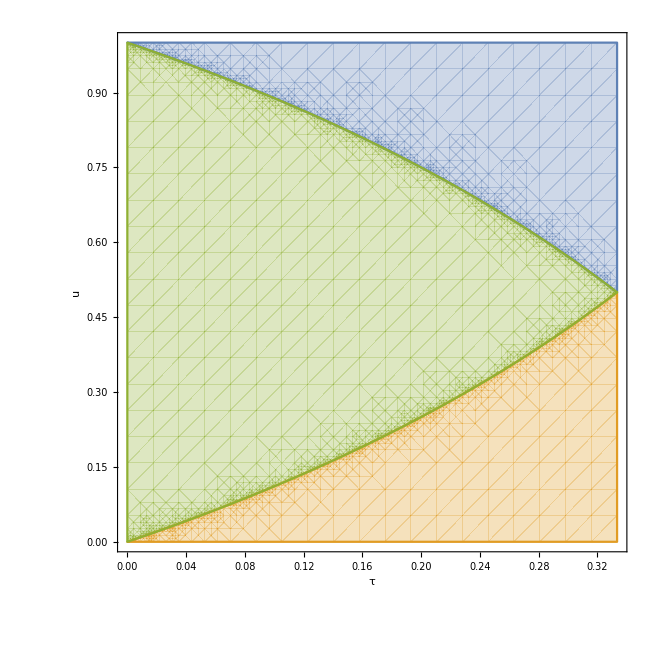

```mathematica
plotMe={ans[[1,1,2]],ans[[1,2,2]],ans[[1,3,2]]}/.tau->tt/.u->uu/.ubar->1-uu
(*plotMe={tau<1}/.tau->tt/.u->uu*)
RegionPlot[plotMe,{tt,0,1/3},{uu,0,1},AxesLabel-> {tau,u},MaxRecursion->5]
```

{1-uu>0∧1-uu<tt,uu>0∧uu<tt,(uu>tt∧2 uu<1)∨(2 uu>1∧1-uu>tt)}

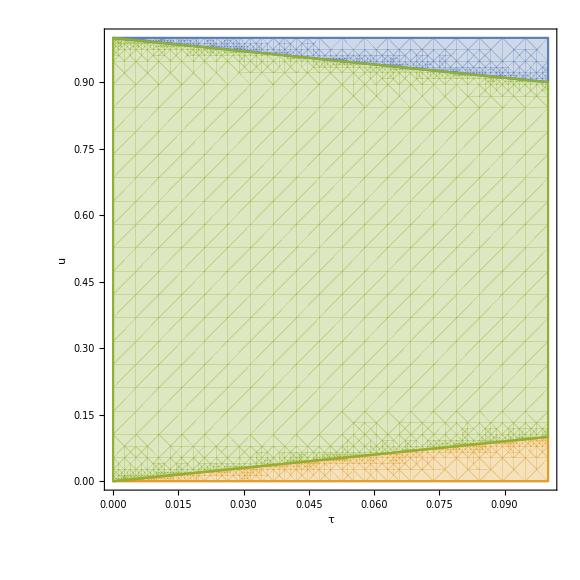

```mathematica
plotMe={ansExpanded[[1,1,2]],ansExpanded[[1,2,2]],ansExpanded[[1,3,2]]}/.tau->tt/.u->uu/.ubar->1-uu
(*plotMe={tau<1}/.tau->tt/.u->uu*)
RegionPlot[plotMe,{tt,0,1/10},{uu,0,1},AxesLabel-> {tau,u},MaxRecursion->5]
```

```mathematica
prefacff=-alphabar(muMS^2*Exp[EulerGamma]/Q^2)^eps/(2Gamma[2+eps]);
ff[w_]:=-w^eps*Series[prefacff*(tau^(1+eps)*HeavisideTheta[w-tau]+w^(1+eps)*HeavisideTheta[tau-w]),{eps,0,0}]//Normal/.eps->0
cc0[uu_,ww_]:=-(1-uu)^2(HeavisideTheta[1/2-uu]DiracDelta[uu-ww]+HeavisideTheta[1/2-(1-uu)]DiracDelta[(1-uu)-ww])
cc1[uu_,ww_]:=(1-uu)^2DiracDelta[uu-ww]
```

```mathematica
dud1=Integrate[ff[w]*cc1[u,w],{w,0,Infinity},Assumptions->0<u<1]
%//Expand
```

1/2 (u-1)^2 ᾱ (τ u-τ+u τ-u)

1/2 u^3 ᾱ τ-u+1/2 τ u^2 ᾱ u-τ-u^2 ᾱ τ-u-τ u ᾱ u-τ+1/2 u ᾱ τ-u+1/2 τ ᾱ u-τ

```mathematica
FullSimplify[ansExpanded/.ubar->1-u,Assumptions->0<u<tau<1/3]
```

(u-1) (-(u-1) u)^(ϵ+1)

```mathematica
dud1*(-1/u)
ray=Integrate[%,{u,0,1}]
```

-((u-1)^2 ᾱ (τ u-τ+u τ-u))/(2 u)

1/12 τ ᾱ ((τ-6) τ+6 log(τ)+3)

```mathematica
Series[ray,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
```

1/4 τ (2 ᾱ log(τ)+ᾱ)

1/4 τ (2 ᾱ log(τ)+ᾱ)

1/4 τ (2 ᾱ log(τ)+ᾱ)

```mathematica
Series[ray,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
Series[%,{tau,0,1}]//Normal
Series[%,{eps,0,0}]//Normal
```

1/12 τ ᾱ ((τ-6) τ+6 log(τ)+3)

1/4 τ (2 ᾱ log(τ)+ᾱ)

1/4 τ (2 ᾱ log(τ)+ᾱ)

1/4 τ (2 ᾱ log(τ)+ᾱ)

«1 more identical outputs»

```mathematica
ansExpanded
```

Piecewise[{{-(ū)^(ϵ+3), ū>0∧ū<τ}, {(-u^3+2 u^2-u) (ū)^ϵ u^ϵ, u>0∧u<τ}, {τ (ū)^(ϵ+2) (-u^ϵ), (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

```mathematica
dud1
```

1/2 (u-1)^2 ᾱ (τ u-τ+u τ-u)

```mathematica
dud1/.HeavisideTheta[a_,b_]:> UnitStep[a,b]//PiecewiseExpand
FullSimplify[%,Assumptions->u≠ 1/2&&tau+u≠1&&u≠tau]
diffCheck=(ansExpanded/. 1+1/(u-2)->ubar/(1+ubar)   )+2%/alphabar

FullSimplify[diffCheck/.ubar->1-u,Assumptions->u<tau<1/3&&0<u<1/2]//PiecewiseExpand
Series[%,{eps,0,0}]//Normal
FullSimplify[diffCheck/.ubar->1-u,Assumptions->0<tau<u&&0<u<1/2]//PiecewiseExpand
Series[%,{eps,0,0}]//Normal
FullSimplify[diffCheck/.ubar->1-u,Assumptions->(1-u)<tau<1/3&&0<(1-u)<1/2]//PiecewiseExpand
Series[%,{eps,0,0}]//Normal
FullSimplify[diffCheck/.ubar->1-u,Assumptions->0<tau<(1-u)&&0<(1-u)<1/2]//PiecewiseExpand
Series[%,{eps,0,0}]//Normal
```

1/2 (u-1)^2 ᾱ (τ u-τ+u τ-u)

1/2 (u-1)^2 ᾱ (τ u-τ+u τ-u)

(Piecewise[{{-(ū)^(ϵ+3), ū>0∧ū<τ}, {u^ϵ (-u^3+2 u^2-u) (ū)^ϵ, u>0∧u<τ}, {-u^ϵ (ū)^(ϵ+2) τ, (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}])+(u-1)^2 (τ u-τ+u τ-u)

-(u-1)^2 u ((-(u-1) u)^ϵ-1)

0

τ (-(u-1)^2) ((-(u-1) u)^ϵ-1)

0

τ (u-1)^2-(1-u)^(ϵ+3)

τ (u-1)^2+(u-1)^3

τ (-(u-1)^2) ((-(u-1) u)^ϵ-1)

0

```mathematica
Series[%,{ubar,0,1}]
```

0

```mathematica
FullSimplify[ans,Assumptions->u>tau&&0<u<1/2]
Series[%,{tau,0,2}]//Normal
Series[%,{eps,0,0}]
Series[%,{tau,0,2}]//Normal
FullSimplify[%*prefac2a1,Assumptions->0<u<1]
```

Piecewise[{{(ū)^(ϵ+2) (-u^ϵ) (ū)/(ū+1)ϵ+12 ϵ+3, τ u+1<2 τ+u}, {(ū)^(ϵ+2) (-u^ϵ) u/(u+1)ϵ+12 ϵ+3, τ (u+1)>u}, {(ū)^(ϵ+2) (-u^ϵ) τϵ+12 ϵ+3, True}}]

Piecewise[{{(ū)^(ϵ+2) (-u^ϵ) u/(u+1)ϵ+12 ϵ+3, ((u==1∨(u==0∧u^2-u<1/2))∧-2 τ+τ u-u≥-1∧τ+τ u-u>0)∨u<0∨(u<1/2∧u^2-u≥1/2)}, {(ū)^(ϵ+2) (-u^ϵ) (ū)/(ū+1)ϵ+12 ϵ+3, ((u==1∨(u==0∧u^2-u<1/2))∧-2 τ+τ u-u<-1)∨u>1}, {τ^ϵ ((2 τ^2 (ϵ+1) (ū)^(ϵ+2) u^ϵ)/(ϵ+2)-(τ (ū)^(ϵ+2) u^ϵ)/(ϵ+1)), True}}]

Piecewise[{{-1/3 (ū)^2 (1-(1-u/(u+1))^3)+O(ϵ^1), (u≤0∧u^2-u<1/2∧-2 τ+τ u-u≥-1∧τ+τ u-u>0)∨(u==1∧-2 τ+τ u-u≥-1∧τ+τ u-u>0)∨u<0∨(u<1/2∧u^2-u≥1/2)}, {-((ū)^3 ((ū)^2+3 ū+3))/(3 (ū+1)^3)+O(ϵ^1), (u==0∧u^2-u<1/2∧-2 τ+τ u-u<-1)∨(u≥1∧-2 τ+τ u-u<-1)∨u>1}, {((ū)^2 τ^2-(ū)^2 τ)+O(ϵ^1), True}}]

Piecewise[{{-1/3 (ū)^2 (1-(1-u/(u+1))^3), (u==1∧-2 τ+τ u-u≥-1∧τ+τ u-u>0)∨(u≤0∧-2 τ+τ u-u≥-1∧τ+τ u-u>0∧u^2-u<1/2)∨u<0∨(u<1/2∧u^2-u≥1/2)}, {-((ū)^3 ((ū)^2+3 ū+3))/(3 (ū+1)^3), (u==0∧u^2-u<1/2∧-2 τ+τ u-u<-1)∨(u≥1∧-2 τ+τ u-u<-1)∨u>1}, {(ū)^2 τ^2-(ū)^2 τ, True}}]

8 g^2 (ū)^2 Q^2 (τ-1) τ (ϵ+1) C_F

```mathematica
rah=FullSimplify[que]
```

que

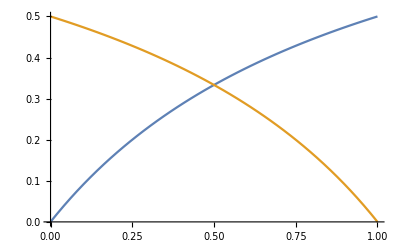

```mathematica
Plot[{x/(1+x),(1-x)/(2-x)},{x,0,1}]
```

```mathematica
(* the soft functions must match onto the above result:

τ (-2 ᾱ log(τ)-ᾱ)

which is what we get from C_2^0dag * C_2^2a1 * <O20a|O22a1> + C_2^0 * C_2^2a1dag * <O22a1|O20a>
*)

softCoeff0 = alphabar*tau(2LJ-7)
softCTerm0=DiracDelta[tau-delta](1-2alphabar(1/eps^2-LQ/eps))+4*alphabar*PlusDistribution[HeavisideTheta[tau]/tau]/eps;
softFinite0=DiracDelta[-δ+τ]-LQ^2*DiracDelta[-δ+τ]*alphabar+(Pi^2*DiracDelta[-δ+τ]*OverBar[α])/6-4*alphabar*(LQ*PlusDistribution[τ^(-1)]+2*PlusDistribution[Log[τ]/τ])
softVev0=softCTerm0+softFinite0-DiracDelta[tau-delta];

Series[softCoeff0*softFinite0//Expand,{alphabar,0,1}]//Normal;
contributionIgrand=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,1}]+Integrate[SeriesCoefficient[contributionIgrand,{DiracDelta[tau-delta],0,0}],{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%*c2*ComplexConjugate[c2]/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont0=Limit[%,delta->0]//expLogs//Expand

checkLO=finalO20aO22a1-check0
(* still missing terms proportional to tau: need subleading soft operators *)





(* soft operator 2M is the same field content with measurement operator Mhat=-kp*km*(D@DiracDelta[tau-kp]Theta[km-kp]+D@DiracDelta[tau-km]Theta[kp-km]) *)
softCoeff2M=0(*7/2*)(* this operator can't contibute *)
softCTerm2M=0;
softFinite2M=-2*alphabar
softVev2M=-2*alphabar;

Series[softCoeff2M*softFinite2M//Expand,{alphabar,0,1}]//Normal;
contributionIgrand2M=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution2M=Integrate[contributionIgrand2M,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2M=Limit[%,delta->0]//expLogs//Expand


(* soft operator 2A1 is W_nb^dag (iD)^2(x+nb*t) W_n^dag W_nb *)
softCoeff2A1=-1
softCTerm2A1=0;(* needs anomalous dimension matrix *)
softFinite2A1=2alphabar(LS-1)
softVev2A1=2alphabar(LS-1-1/eps);

Series[softCoeff2A1*softFinite2A1//Expand,{alphabar,0,1}]//Normal
contributionIgrand2A1=%//replShortLogs/.PlusDistribution[a_]:>PlusDistribution[a*HeavisideTheta[tau]]//replSingVarPlus//expLogs//Expand;

softContribution0=Integrate[contributionIgrand2A1,{tau,0,tau+2delta},Assumptions->beta>0&&delta>0];
Limit[FullSimplify[%,Assumptions->0<delta<tau&&0<beta<tau],delta->0]//FullSimplify;

Series[%/.alphaMS->alphabar*2*Pi/Cf,{alphabar,0,1}]//Normal;
cont2A1=Limit[%,delta->0]//expLogs//Expand

checkNLO=finalO20aO22a1-cont0-cont2A1-cont2M//Expand
```

(2 LJ-7) τ ᾱ

1/6 π^2 ᾱ τ-δ+LQ^2 ᾱ (-τ-δ)-4 ᾱ (LQ (1/τ)_++2 ((log(τ))/τ)_+)+τ-δ

-7 τ ᾱ+2 τ ᾱ log(τ)-4 τ ᾱ log(μ_OverBar[MS])+4 τ ᾱ log(Q)

finalO20aO22a1-check0

0

-2 ᾱ

0

-1

2 (LS-1) ᾱ

(2-2 LS) ᾱ

6 τ ᾱ-4 τ ᾱ log(τ)+4 τ ᾱ log(μ_OverBar[MS])-4 τ ᾱ log(Q)

τ ᾱ+2 τ ᾱ log(τ)+finalO20aO22a1

```mathematica
(* for figuring out matching coefficients *)
eq1=SeriesCoefficient[checkNLO,{Log[muMS],0,1}]
eq2=SeriesCoefficient[checkNLO,{Log[tau],0,1}]
eq3=SeriesCoefficient[checkNLO,{Log[_],0,0}]

Solve[{eq1,eq2,eq3}=={0,0,0},{A,B,R}]
```

0

2 τ ᾱ

τ ᾱ+finalO20aO22a1

{}

#### < O20a | O22a2 > + < O22a2 | O20a >

```mathematica
ampO20aO22a2=(GSD[p2].ampDagO20a.GSD[p1].ampO22a2+GSD[p2].ampDagO22a2.GSD[p1].ampO20a)*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO20aO22a2=Tr[%]//FCE//DiracSimplify//FCE  ; 

dTraceO20aO22a2//regAkinematics;
%//Simplify;
%/.D->4-2*eps//Simplify;
O20aO22a2finite=Series[%,{eps,0,1}]//Normal;

krabbyO20aO22a2=O20aO22a2finite/.eps->negeps/.negeps->-eps   (* flip the epsilon here *)

(* 
from here recognize c00, c01, c02, c10, c11, c12, c20,c21,c22,etc. 
*)
O20aO22a200=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,0}];
O20aO22a210=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,0}];
O20aO22a220=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,0}];
O20aO22a230=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,0}];

O20aO22a201=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,1}];
O20aO22a211=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,1}];
O20aO22a221=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,1}];
O20aO22a231=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,1}];

O20aO22a202=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,2}];
O20aO22a212=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,2}];
O20aO22a222=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,2}];
O20aO22a232=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,2}];

O20aO22a203=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,0},{x13,0,3}];
O20aO22a213=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,1},{x13,0,3}];
O20aO22a223=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,2},{x13,0,3}];
O20aO22a233=SeriesCoefficient[krabbyO20aO22a2*x13*x23,{x23,0,3},{x13,0,3}];

coeffArrO20aO22a2={{O20aO22a200,O20aO22a201,O20aO22a202,O20aO22a203},{O20aO22a210,O20aO22a211,O20aO22a212,O20aO22a213},{O20aO22a220,O20aO22a221,O20aO22a222,O20aO22a223},{O20aO22a230,O20aO22a231,O20aO22a232,O20aO22a233}}
checksumO20aO22a2=krabbyO20aO22a2*x13*x23-({1,x23,x23^2,x23^3}.coeffArrO20aO22a2.{1,x13,x13^2,x13^3})//FullSimplify


(* contribution from region A *)

totalO20aO22a2=0;
totalO20aO22a2+=O20aO22a200*regA00+O20aO22a201*regA01+O20aO22a202*regA02+O20aO22a203*regA03;
totalO20aO22a2+=O20aO22a210*regA10+O20aO22a211*regA11+O20aO22a212*regA12+O20aO22a213*regA13;
totalO20aO22a2+=O20aO22a220*regA20+O20aO22a221*regA21+O20aO22a222*regA22+O20aO22a223*regA23;
totalO20aO22a2+=O20aO22a230*regA30+O20aO22a231*regA31+O20aO22a232*regA32+O20aO22a233*regA33;
totalO20aO22a2=totalO20aO22a2/.eps->negeps/.negeps->-eps//FullSimplify  (* and flip the epsilon back here *)


contributionO20aO22a2=phaseSpacePrefac*totalO20aO22a2;
%/.g->Sqrt[4*Pi*alphaMS*(Exp[EulerGamma]muMS^2/(4Pi) )^eps];
Series[%,{alphaMS,0,1}]//Normal;
Series[%,{eps,0,0}]//Normal;
contributionO20aO22a2=%//Expand
```

8 ϵ (g^2 Q^2 (-C_F) u1+x23/(1-x13)-1+g^2 Q^2 x13 C_F u1+x23/(1-x13)-1+g^2 Q^2 x23 C_F u1+x23/(1-x13)-1-g^2 Q^2 C_F u2+x23/(1-x13)-1+g^2 Q^2 x13 C_F u2+x23/(1-x13)-1+g^2 Q^2 x23 C_F u2+x23/(1-x13)-1)

(0 | 0 | 0 | 0
0 | -8 C_F g^2 ϵ u1-1 Q^2-8 C_F g^2 ϵ u2-1 Q^2 | 8 C_F g^2 ϵ u1-1 Q^2+8 C_F g^2 ϵ u2-1 Q^2 | 0
0 | 8 C_F g^2 ϵ u1-1 Q^2+8 C_F g^2 ϵ u2-1 Q^2-8 C_F g^2 ϵ δ'(u1-1) Q^2-8 C_F g^2 ϵ δ'(u2-1) Q^2 | 0 | 0
0 | 8 C_F g^2 ϵ δ'(u1-1) Q^2+8 C_F g^2 ϵ δ'(u2-1) Q^2-4 C_F g^2 ϵ δ''(u1-1) Q^2-4 C_F g^2 ϵ δ''(u2-1) Q^2 | 8 C_F g^2 ϵ δ'(u1-1) Q^2+8 C_F g^2 ϵ δ'(u2-1) Q^2-4 C_F g^2 ϵ δ''(u1-1) Q^2-4 C_F g^2 ϵ δ''(u2-1) Q^2 | 8 C_F g^2 ϵ δ'(u1-1) Q^2+8 C_F g^2 ϵ δ'(u2-1) Q^2-4 C_F g^2 ϵ δ''(u1-1) Q^2-4 C_F g^2 ϵ δ''(u2-1) Q^2)

-x13^2 (x23 (8 g^2 Q^2 ϵ C_F u1-1+8 g^2 Q^2 ϵ C_F u2-1)+x23^3 (8 g^2 Q^2 ϵ C_F δ'(u1-1)-4 g^2 Q^2 ϵ C_F δ''(u1-1)+8 g^2 Q^2 ϵ C_F δ'(u2-1)-4 g^2 Q^2 ϵ C_F δ''(u2-1)))-x13 (x23^2 (8 g^2 Q^2 ϵ C_F u1-1+8 g^2 Q^2 ϵ C_F u2-1-8 g^2 Q^2 ϵ C_F δ'(u1-1)-8 g^2 Q^2 ϵ C_F δ'(u2-1))+x23 (-8 g^2 Q^2 ϵ C_F u1-1-8 g^2 Q^2 ϵ C_F u2-1)+x23^3 (8 g^2 Q^2 ϵ C_F δ'(u1-1)-4 g^2 Q^2 ϵ C_F δ''(u1-1)+8 g^2 Q^2 ϵ C_F δ'(u2-1)-4 g^2 Q^2 ϵ C_F δ''(u2-1)))+8 x13 x23 ϵ (g^2 Q^2 (-C_F) u1+x23/(1-x13)-1+g^2 Q^2 x13 C_F u1+x23/(1-x13)-1+g^2 Q^2 x23 C_F u1+x23/(1-x13)-1-g^2 Q^2 C_F u2+x23/(1-x13)-1+g^2 Q^2 x13 C_F u2+x23/(1-x13)-1+g^2 Q^2 x23 C_F u2+x23/(1-x13)-1)-x13^3 x23^3 (8 g^2 Q^2 ϵ C_F δ'(u1-1)-4 g^2 Q^2 ϵ C_F δ''(u1-1)+8 g^2 Q^2 ϵ C_F δ'(u2-1)-4 g^2 Q^2 ϵ C_F δ''(u2-1))

1/2 τ (-8 g^2 Q^2 ϵ C_F u1-1-8 g^2 Q^2 ϵ C_F u2-1+8 g^2 Q^2 ϵ C_F δ'(u1-1)+8 g^2 Q^2 ϵ C_F δ'(u2-1))+τ (8 g^2 Q^2 ϵ C_F u1-1+8 g^2 Q^2 ϵ C_F u2-1)+1/3 τ (-8 g^2 Q^2 ϵ C_F δ'(u1-1)+4 g^2 Q^2 ϵ C_F δ''(u1-1)-8 g^2 Q^2 ϵ C_F δ'(u2-1)+4 g^2 Q^2 ϵ C_F δ''(u2-1))

0

```mathematica
contributionO20aO22a2/.alphaMS->alphabar*2*Pi/Cf//Expand
%//expLogs
%/.Log[-Q^2+I*delta]->2Log[Q]+I*Pi/.Log[-Q^2-I*delta]->2Log[Q]-I*Pi
finalO20aO22a2=Series[%,{tau,0,1}]//Normal
```

0

0

0

«1 more identical outputs»

#### < O21a | O21a >

```mathematica
(*ampO21aO21a=(GSD[p2].ampDagO21a.GSD[p1].ampO21a(*+GSD[p2].ampDagO22a1.GSD[p1].ampO20a *))*spinSum/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;*)
ampO21aO21a=(GSD[p2].ampDagO21a.GSD[p1].ampO21a(*+GSD[p2].ampDagO22a1.GSD[p1].ampO20a *))*MTD[alpha,beta]/.SpinorUBar[p1].a_:>a/.a_ .SpinorU[p1]:>a/.SpinorVBar[p2].a_:>a/.a_ .SpinorV[p2]:>a;

%//DiracSimplify//FCE;
%/.Ta*Tb->Cf//PhatDef//lcCompAll;
%/.Vperp[p1]->-Vperp[q]/.Vperp[p2]->0//Contract//DiracSimplify//FCE;
%//gPerpDef;
dTraceO21aO21a=Tr[%]//FCE//DiracSimplify//FCE  

dTraceO21aO21a//regAkinematics;
%//Simplify;
%/.D->4+2*eps//Simplify;
O21aO21afinite=(Series[%,{eps,0,1}]//Normal)/.DiracDelta[u2+a_]:>Inactive[DiracDelta][u2+a]

Integrate[%*(x13*x23*(1-x13-x23))^eps,{x23,x13,1-2*x13}]
(*Integrate[%*(1-x13)^(1+2*eps)(x13*qhatm*(1-qhatm))^eps,{qhatm,x13/(1-x13),1-x13/(1-x13)}]*)
halfO21aO21a=FullSimplify[%,Assumptions->0<u1<1&&0<u2<1&&0<x13<1/3]
```

1/4 (16-8 D) g^2 p_2^+ p_1^- C_F n^ν (n̄)^μ u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- C_F n^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- (-C_F) n^μ n^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^--1/4 (16-8 D) g^2 p_2^+ p_1^- C_F (n̄)^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-

4 g^2 Q^2 C_F n^ν (n̄)^μ (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]+4 g^2 Q^2 C_F n^μ (n̄)^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]+ϵ (4 g^2 Q^2 C_F n^ν (n̄)^μ (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]+4 g^2 Q^2 C_F n^μ (n̄)^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]-4 g^2 Q^2 C_F n^μ n^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]-4 g^2 Q^2 C_F (n̄)^μ (n̄)^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)])-4 g^2 Q^2 C_F n^μ n^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]-4 g^2 Q^2 C_F (n̄)^μ (n̄)^ν (x13+x23-1) u1+x23/(x13-1) δ[u2+x23/(x13-1)]

$Aborted

$Aborted

```mathematica
dTraceO21aO21a
(16-8D)*(-FVD[nb-n,mu]FVD[nb-n,nu]/4)g^2*p2p*p1m*Cf*DiracDelta[u2-qhatm]DiracDelta[u1-qhatm]//gPerpDef
%-dTraceO21aO21a//Expand
```

1/4 (16-8 D) g^2 p_2^+ p_1^- C_F n^ν (n̄)^μ u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- C_F n^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- (-C_F) n^μ n^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^--1/4 (16-8 D) g^2 p_2^+ p_1^- C_F (n̄)^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-

1/4 (16-8 D) g^2 p_2^+ p_1^- C_F u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^- (n^μ-(n̄)^μ) ((n̄)^ν-n^ν)

0

```mathematica
Tr[GAD[tau].GSD[k].GAD[tau].GSD[k]]
```

-4 (D-2) k^2

```mathematica
dTraceO21aO21a
Collect2[%,FVD[nb-n,mu]]
```

1/4 (16-8 D) g^2 p_2^+ p_1^- C_F n^ν (n̄)^μ u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- C_F n^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- (-C_F) n^μ n^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^--1/4 (16-8 D) g^2 p_2^+ p_1^- C_F (n̄)^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-

1/4 (16-8 D) g^2 p_2^+ p_1^- C_F n^ν (n̄)^μ u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- C_F n^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-+(4-2 D) g^2 p_2^+ p_1^- (-C_F) n^μ n^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^--1/4 (16-8 D) g^2 p_2^+ p_1^- C_F (n̄)^μ (n̄)^ν u1-OverHat[TraditionalForm`TraditionalForm`q]^- u2-OverHat[TraditionalForm`TraditionalForm`q]^-

```mathematica
dTr
```

```mathematica
halfO21aO21a//PiecewiseExpand
```

Piecewise[{{16 g^2 Q^2 (u1-1) (x13-1)^2 (ϵ+1) C_F (1-x13)^(2 ϵ) ((1-u1) u1 x13)^ϵ δ[u2-u1], u1 x13-u1-2 x13>-1∧u1 x13-u1+x13<0}, {0, True}}]

```mathematica
prefac1a1a=16g^2*Cf*Q^2*(eps+1)*(u1-1)*(u1*(1-u1))^eps*Inactive[DiracDelta][u2-u1]
halfO21aO21a//Expand//PiecewiseExpand
%/prefac1a1a/.HeavisideTheta[a_,b_]:>Boole[a>0&&b>0]
FullSimplify[%,Assumptions->0<u1<1&&0<x13<1/3]

(*integrateTermByTerm[%,{x13,0,tau}]/.u1->u*)
Integrate[%,{x13,0,tau}]/.u1->u/. 1-u->ubar/.u-1->-ubar
ans1a1a=FullSimplify[%]/. 1+1/(u-2)->ubar/(1+ubar)
ans1a1aExpanded=ans1a1a/.tau*u+1<2*tau+u-> ubar<tau/.u<1->ubar>0/.u<tau+tau*u->u<tau/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]
ans1a1aExpanded1=ans1a1a/.tau*u+1<2*tau+u-> ubar<tau/.tau*u+1≥ 2*tau+u-> ubar>tau/.u<tau+tau*u->u<tau/.tau+tau*u≤u->u>tau/.u<1->ubar>0/. (2u== 1)&&a_:>a
ans1a1aExpanded2=FullSimplify[ans1a1aExpanded1/.Beta[ubar/(1+ubar),eps+1,2eps+3]->Normal@Series[Beta[ubar/(1+ubar),eps+1,2eps+3],{eps,0,0},{ubar,0,1}]/.Beta[u/(1+u),eps+1,2eps+3]->Normal@Series[Beta[u/(1+u),eps+1,2eps+3],{eps,0,0},{u,0,1}]/.Beta[tau,eps+1,2eps+3]->Normal@Series[Beta[tau,eps+1,2eps+3],{eps,0,0},{tau,0,1}],Assumptions->2u≠1]
```

16 g^2 Q^2 (u1-1) (ϵ+1) C_F ((1-u1) u1)^ϵ δ[u2-u1]

Piecewise[{{16 g^2 Q^2 (u1-1) (x13-1)^2 (ϵ+1) C_F (1-x13)^(2 ϵ) ((1-u1) u1 x13)^ϵ δ[u2-u1], u1 x13-u1-2 x13>-1∧u1 x13-u1+x13<0}, {0, True}}]

Piecewise[{{(x13-1)^2 ((1-u1) u1)^-ϵ (1-x13)^(2 ϵ) ((1-u1) u1 x13)^ϵ, u1 x13-u1-2 x13>-1∧u1 x13-u1+x13<0}, {0, True}}]

Piecewise[{{(1-x13)^(2 (ϵ+1)) x13^ϵ, u1 x13+1>u1+2 x13∧u1 x13+x13<u1}, {0, True}}]

Piecewise[{{1/(u-2)+1ϵ+12 ϵ+3, 1/2<u<1∧τ-u/(u-2)+1/(u-2)>0∧τ<1/3}, {u/(u+1)ϵ+12 ϵ+3, 0<u<1/2∧u/(u+1)-τ<0∧τ<1/3}, {τϵ+12 ϵ+3, (0<u<1/2∧τ>0∧u/(u+1)-τ≥0)∨(u==1/2∧0<τ<1/3)∨(1/2<u<1∧τ>0∧τ-u/(u-2)+1/(u-2)≤0)}}]

Piecewise[{{(ū)/(ū+1)ϵ+12 ϵ+3, u<1∧τ u+1<2 τ+u}, {u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ+τ u}, {τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{ū, ū>0∧ū<τ}, {u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {τϵ+12 ϵ+3, 2 u==1∨(τ+τ u≤u∧2 u<1)∨(2 u>1∧τ u+1≥2 τ+u)}}]

Piecewise[{{(ū)/(ū+1)ϵ+12 ϵ+3, ū>0∧ū<τ}, {u/(u+1)ϵ+12 ϵ+3, u>0∧u<τ}, {τϵ+12 ϵ+3, 2 u==1∨(u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

Piecewise[{{ū, ū>0∧ū<τ}, {u, u>0∧u<τ}, {τ, (u>τ∧2 u<1)∨(2 u>1∧ū>τ)}}]

```mathematica
ans1a1aExpanded=PiecewiseExpand[ans1a1aExpanded2*prefac1a1a/.u1->u/.u-1->-ubar]/.ubar^(eps+3)*(-u^eps)->ubar^eps*Normal@Series[ubar^3*(-u^eps)/.u->1-ubar,{ubar,0,3}]/.-ubar*(ubar*u)^(eps+1)->ubar^eps*Normal@Series[-ubar^2*u^(eps+1)/.ubar->1-u,{u,0,3}]//FullSimplify
```

Piecewise[{{-16 g^2 (ū)^2 Q^2 (ϵ+1) C_F ((1-u) u)^ϵ δ[u2-u], ū>0∧ū-τ<0}, {-16 g^2 ū Q^2 u (ϵ+1) C_F ((1-u) u)^ϵ δ[u2-u], u>0∧u-τ<0}, {-16 g^2 ū Q^2 τ (ϵ+1) C_F ((1-u) u)^ϵ δ[u2-u], (u>1/2∧ū-τ>0)∨(u<1/2∧u-τ>0)}}]

#### Reg A Sum

```mathematica
finalO20aO20a+finalO20aO21a+finalO20aO22a1+finalO20aO22a2+finalO21aO21a
%//FullSimplify
%//Expand

(*%/.Log[Q/muMS]->L0/2
%/.Log[Q^6/(tau^3*muMS^6)]->3(L0-LT)/.Log[tau]->LT
%//FullSimplify
%//Expand
%/.LT^2->(L0^2+L2^2-2L1^2)/2
%//Expand*)
```

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-3 ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ+1/6 τ (-2 Q^2 ᾱ u1-2 Q^2 ᾱ u2-Q^2 ᾱ δ'(u1)-Q^2 ᾱ δ''(u1)-Q^2 ᾱ δ'(u2)-Q^2 ᾱ δ''(u2))+1/3 τ (Q^2 ᾱ u2 δ'(u1)+Q^2 ᾱ u1 δ'(u2)-Q^2 ᾱ u2 δ''(u1)-Q^2 ᾱ u1 δ''(u2)-3 Q^2 ᾱ u1 u2-2 Q^2 ᾱ δ'(u1) δ'(u2))-8 ᾱ log(Q) log(μ_OverBar[MS])+4 ᾱ log^2(μ_OverBar[MS])+6 ᾱ log(μ_OverBar[MS])+4 ᾱ log^2(Q)-6 ᾱ log(Q)+1

1/6 τ (-2 Q^2 ᾱ u1-2 Q^2 ᾱ u2-Q^2 ᾱ δ'(u1)-Q^2 ᾱ δ''(u1)-Q^2 ᾱ δ'(u2)-Q^2 ᾱ δ''(u2))+1/3 τ (Q^2 ᾱ u2 δ'(u1)+Q^2 ᾱ u1 δ'(u2)-Q^2 ᾱ u2 δ''(u1)-Q^2 ᾱ u1 δ''(u2)-3 Q^2 ᾱ u1 u2-2 Q^2 ᾱ δ'(u1) δ'(u2))+ᾱ (log(μ_OverBar[MS]^6/(Q^6 τ^3))+4 log^2(Q/μ_OverBar[MS])-4 τ-2 log^2(τ)+8 τ log(τ)-(5 π^2)/6+7)+1

-4 τ ᾱ-2 ᾱ log^2(τ)+8 τ ᾱ log(τ)-(5 π^2 ᾱ)/6+7 ᾱ-1/3 Q^2 τ ᾱ u1+1/3 Q^2 τ ᾱ u2 δ'(u1)+1/3 Q^2 τ ᾱ u1 δ'(u2)-1/3 Q^2 τ ᾱ u2 δ''(u1)-1/3 Q^2 τ ᾱ u1 δ''(u2)-Q^2 τ ᾱ u1 u2-1/3 Q^2 τ ᾱ u2+ᾱ log(μ_OverBar[MS]^6/(Q^6 τ^3))+4 ᾱ log^2(Q/μ_OverBar[MS])-1/6 Q^2 τ ᾱ δ'(u1)-1/6 Q^2 τ ᾱ δ''(u1)-2/3 Q^2 τ ᾱ δ'(u1) δ'(u2)-1/6 Q^2 τ ᾱ δ'(u2)-1/6 Q^2 τ ᾱ δ''(u2)+1